-Graphics-

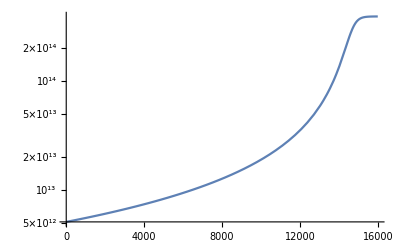

out.xls

```mathematica
ClearAll["Global`*"]
(**Code for Computing the Multiphase Kinetics of Trace gas (X) reacting with  solute Y in a droplet.
	by Kevin Wilson, Lawrence Berkeley National Laboratory**)
(**Parameters based upon the ozonolysis (X) of trans-aconitic acid (Y) as described in Coupled Interfacial and Bulk Kinetics Govern the Timescales of Multiphase Ozonolysis Reactions Megan D. Willis and Kevin R. Wilson Journal of Physical Chemistry A 2022 126 (30),4991-5010 DOI:10.1021/acs.jpca.2c03059 **)

(**Droplet Parameters**)
	r = 9.23×10^-4;(** Droplet radius in cm**)
	δ=1×10^-7; (**Interface thickness in cm**)
	Subscript[V, SB]=(r^3-(r-δ)^3)/r^3;(**Bulk volume to interface volume ratio in droplet**)

(**X+Y Rate Coefficients**)
	Subscript[k, brxn] =1.4×10^-17;(**Bulk reaction rate coefficient in cm^3/(molec.s)**)
	Subscript[k, srxn] =1.4×10^-17;(**Surface reaction rate coefficient in cm^3/(molec.s)**)

(**Trace Gas X Parameters**)
	Subscript[k, Xads]=9.0×10^-15;(**Adsorption rate coefficient for X in cm^3/(molec.s)**)
	Subscript[k, Xdes]=5.4×10^6;(**Desorption rate coefficient for X in s^-1**)
	Subscript[k, Xsolv]= 4.58×10^5 ;(**Solvation rate coefficient for X in s^-1**)
	Subscript[k, Xdesolv]= 2.80×10^-15; (**Desolvation rate coefficient for Y in cm^3/(molec.s)**)
	Subscript[Γ, ∞X]= 5.42×10^14;(**Maximium surface concentration of X in molec. cm^-2**)
	Subscript[H, gb]=0.272;(**Dimensionless Henry's Law, gas-bulk**)
	Subscript[H, gs]=8.98;(**Dimensionless Henry's Law, gas-surface**)
	Subscript[X, g]=1.43×10^15; (**Concentration of Gas phase X in molec. cm^-3**)
	Subscript[D, x] = 1.76 ×10^-5;(**Liquid phase diffusion constant of X in cm^2/s **)
	
(**Solute Y Parameters**)
	Subscript[k, Ysolv]= 90 ;(**Solvation rate coefficient for Y in s^-1**)
	Subscript[k, Ydesolv]= 1.2×10^-20 ;(**Desolvation rate coefficient for Y in cm^3/(molec.s)**)
	 Subscript[K, eq] =Subscript[k, Ydesolv]/Subscript[k, Ysolv]; (**Langmuir equillbrium constant in cm^3/molec.**)
	Subscript[Γ, ∞Y]= 1.54×10^14; (**Maximium surface concentration of Y in molec. cm^-2**)
	Subscript[Y, 0]=1.9×10^21; (**Intial Concentration of Y in droplet in in molec. cm^-3**)


(**Transport Parameters**)
	Subscript[k, diffusion] =(2 Subscript[D, x])/(r/3)^2;
	Subscript[r, gs] =3×√((2 Subscript[D, x])/(Subscript[k, Xads] Subscript[X, g]+Subscript[k, Xdes]));(**Critical radius gas-surface in cm**)
	Subscript[r, sb] =3×√((2 Subscript[D, x])/(Subscript[k, Xdesolv] Subscript[H, gb] Subscript[X, g]+Subscript[k, Xsolv])) ;(**Critical radius surface-bulk in cm**)
	R= r/(r+Subscript[r, gs]+Subscript[r, sb]); (**Weighting function**)
	Subscript[k, sb]=(1/(Subscript[k, diffusion]×R)+1/(Subscript[k, Xsolv]×(1-R)))^-1;Subscript[k, gs]=(1/(Subscript[k, diffusion]×R)+1/(Subscript[k, Xdes]×(1-R)))^-1;

	Subscript[k, transport]=(Subscript[k, gs]+Subscript[k, sb])/2 ;(**Subscript[k, transport] includes both diffusive and kinetic contributions**)

(**Lambert W Functions (ProductLog in Mathematica) for Computing Bulk, Surface and Surface+Bulk Kinetics of X and Y**)

	Subscript[Y, Bulk]=Subscript[k, transport]/Subscript[k, brxn] ProductLog[(Subscript[k, brxn]×Subscript[Y, 0])/Subscript[k, transport] ⅇ^((Subscript[k, brxn]×Subscript[Y, 0])/Subscript[k, transport]-Subscript[k, brxn]×Subscript[H, gb]×Subscript[X, g] ×t)];(**Lambert W: Bulk Reactions Only**)

	Subscript[Y, Surface]=1/Subscript[K, eq] ProductLog[Subscript[K, eq]×Subscript[Y, 0] ⅇ^(Subscript[K, eq]×Subscript[Y, 0]-Subscript[k, srxn]×Subscript[H, gs]×Subscript[X, g]×Subscript[Γ, ∞Y]/δ Subscript[K, eq]×Subscript[V, SB]×t)];(**Lambert W: Surface Reactions Only**)
	Subscript[Y, Surf+Bulk]=1/Subscript[K, eq] ProductLog[Subscript[K, eq]×Subscript[Y, Bulk]×ⅇ^(Subscript[K, eq]×Subscript[Y, Bulk]-Subscript[k, srxn]×Subscript[H, gs]×Subscript[X, g]×Subscript[Γ, ∞Y]/δ Subscript[K, eq]×Subscript[V, SB]×t)];(**Lambert W: Surface + Bulk Reactions**)
	Subscript[X, Bulk]=(Subscript[k, transport] Subscript[H, gb] Subscript[X, g])/(Subscript[k, brxn] Subscript[Y, Surf+Bulk]+Subscript[k, transport]);(**Function to compute kinetics of X(b) in the bulk liquid**)

(**Plotting and Saving Result**)
	Plot[ {Subscript[Y, Bulk],Subscript[Y, Surface],Subscript[Y, Surf+Bulk]},{t,0,20000},PlotLegends->"Expressions"]
	LogPlot[ {Subscript[X, Bulk]},{t,0,16000},PlotLegends->"Expressions"]
	out= Table[{t,Subscript[X, Bulk], Subscript[Y, Bulk],Subscript[Y, Surface],Subscript[Y, Surf+Bulk]},{t,0,15000, 10}];
	Export["out.xls",out]
```